```mathematica
(*reading in the data stored from the code bending11.m from MATLAB*)
```

```mathematica
SetDirectory["/Users/emad/Documents/GitHub/McVittie"];
```

```mathematica
Subscript[ψ, E]=Import["euclid04.csv"];
```

```mathematica
Subscript[ψ, comov]=Import["comovpsi04.csv"];
```

```mathematica
Subscript[ψ, stat]=Import["statpsi04.csv"];
```

```mathematica
angularspeed=Import["angular.csv"];
```

```mathematica
uphi=Table[0,{i,3},{j,9}];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,uphi[[i,j]]=angularspeed[[i,j]]]]
```

```mathematica
ff=Table[0,{i,3},{j,9}];
```

```mathematica
f=Import["fvalue.csv"];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,ff[[i,j]]=f[[i,j]]]]
```

```mathematica
hubble=Table[0,{i,3},{j,9}];
```

```mathematica
H=Import["hubble.csv"];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,hubble[[i,j]]=H[[i,j]]]]
```

```mathematica
ur=Table[0,{i,3},{j,9}];
```

```mathematica
speed=Import["speed.csv"];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,ur[[i,j]]=speed[[i,j]]]]
```

```mathematica
ut=Table[0,{i,3},{j,9}];
```

```mathematica
tspeed=Import["speed.csv"];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,ut[[i,j]]=tspeed[[i,j]]]]
```

```mathematica
r=Table[0,{i,3},{j,9}];
```

```mathematica
position=Import["position.csv"];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,r[[i,j]]=position[[i,j]]]]
```

```mathematica
(*********************************)
(*calculations from the datat*)
W=Table[0,{i,3},{j,9},{k,4}];
K=Table[0,{i,3},{j,9},{k,4}];
U1=Table[0,{i,3},{j,9},{k,4}];
U2=Table[0,{i,3},{j,9},{k,4}];
metric=Table[Table[0,{i,4},{j,4}],{k,3},{l,9}];
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,W[[i,j]]={1,√ff[[i,j]](r[[i,j]]*hubble[[i,j]]+√ff[[i,j]]),0,0}]]
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,K[[i,j]]={ut[[i,j]],ur[[i,j]],0,uphi[[i,j]]}]]
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,U1[[i,j]]={1/(√ff[[i,j]]),r[[i,j]]*hubble[[i,j]],0,0}]]
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,U2[[i,j]]={1/(√(ff[[i,j]]-r[[i,j]]^2*hubble[[i,j]]^2)),0,0,0}]]
```

```mathematica
For[i=1,i<4,i++,For[j=1,j<10,j++,metric[[i,j]]={{-(ff[[i,j]]-r[[i,j]]^2*hubble[[i,j]]^2),-r[[i,j]]*hubble[[i,j]]/(√ff[[i,j]]),0,0},{-r[[i,j]]*hubble[[i,j]]/(√ff[[i,j]]),1/ff[[i,j]],0,0},{0,0,0,0},{0,0,0,r[[i,j]]^2}}]]
```

```mathematica
KdotW=Table[0,{i,3},{j,9}];
U1dotW=Table[0,{i,3},{j,9}];
U1dotK=Table[0,{i,3},{j,9}];
U2dotW=Table[0,{i,3},{j,9}];
U2dotK=Table[0,{i,3},{j,9}];
```

```mathematica
(*cosine calculations*)
For[i=1,i<4,i++,For[j=1,j<10,j++,KdotW[[i,j]]=Simplify[Sum[metric[[i,j,l,m]]*K[[i,j,l]]*W[[i,j,m]],{l,1,4},{m,1,4}]]]]
(****)
For[i=1,i<4,i++,For[j=1,j<10,j++,U1dotW[[i,j]]=Simplify[Sum[metric[[i,j,l,m]]*U1[[i,j,l]]*W[[i,j,m]],{l,1,4},{m,1,4}]]]]
(****)
For[i=1,i<4,i++,For[j=1,j<10,j++,U1dotK[[i,j]]=Simplify[Sum[metric[[i,j,l,m]]*K[[i,j,l]]*U1[[i,j,m]],{l,1,4},{m,1,4}]]]]
(****)
For[i=1,i<4,i++,For[j=1,j<10,j++,U2dotW[[i,j]]=Simplify[Sum[metric[[i,j,l,m]]*U2[[i,j,l]]*W[[i,j,m]],{l,1,4},{m,1,4}]]]]
(****)
For[i=1,i<4,i++,For[j=1,j<10,j++,U2dotK[[i,j]]=Simplify[Sum[metric[[i,j,l,m]]*K[[i,j,l]]*U2[[i,j,m]],{l,1,4},{m,1,4}]]]]
(*************************************************)
thet1=Table[0,{i,3},{j,9}];
thet2=Table[0,{i,3},{j,9}];

For[i=1,i<4,i++,For[j=1,j<10,j++,thet1[[i,j]]=180/Pi*ArcCos[KdotW[[i,j]]/(U1dotK[[i,j]]*U1dotW[[i,j]])+1]]]
For[i=1,i<4,i++,For[j=1,j<10,j++,thet2[[i,j]]=180/Pi*ArcCos[KdotW[[i,j]]/(U2dotK[[i,j]]*U2dotW[[i,j]])+1]]]
```

```mathematica
Needs["PlotLegends`"]
```

LegendPosition::shdw: Symbol LegendPosition appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendShadow::shdw: Symbol LegendShadow appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendSize::shdw: Symbol LegendSize appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendTextSpace::shdw: Symbol LegendTextSpace appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

PlotLegend::shdw: Symbol PlotLegend appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(*Euclidean Bending angle*)
Needs["PlotLegends`"]
```

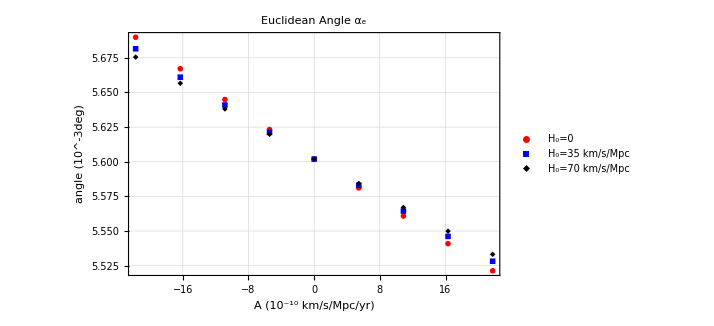

```mathematica
ListPlot[{Table[{1.08711*(5n-25),10^3*(Subscript[ψ, E][[1,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, E][[2,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, E][[3,n]])},{n,1,9}]
},PlotStyle->{Red,Blue,Black},PlotLegends->Placed[{"H_0=0","H_0=35 km/s/Mpc","H_0=70 km/s/Mpc","H_0=105 km/s/Mpc"},{0.9,.8}],AxesLabel->{"A (10^-10 km/s/Mpc/yr)","angle  (10^-3deg)"},PlotLabel->"Euclidean Angle α_e" ,PlotMarkers->{Automatic,Small},GridLines->Automatic,Frame->True,GridLinesStyle->Directive[Gray, Dashed]]
```

```mathematica
(*Comoving Bending angle)
```

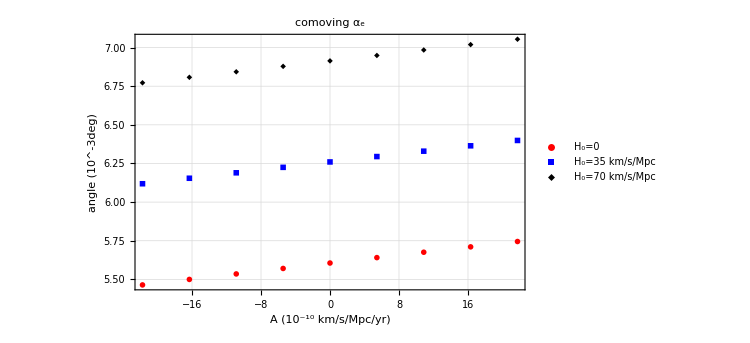

```mathematica
ListPlot[{Table[{1.08711*(5n-25),10^3*(Subscript[ψ, comov][[1,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, comov][[2,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, comov][[3,n]])},{n,1,9}]
},AxesLabel->{"A (10^-10 km/s/Mpc/yr)","angle  (10^-3deg)"},PlotLabel->"comoving α_e" ,PlotLegends->Placed[{"H_0=0","H_0=35 km/s/Mpc","H_0=70 km/s/Mpc","H_0=105 km/s/Mpc"},{0.9,.8}], PlotMarkers->{Automatic,Small},GridLines->Automatic,Frame->True,PlotStyle->{Red,Blue,Black},GridLinesStyle->Directive[Gray, Dashed]]
```

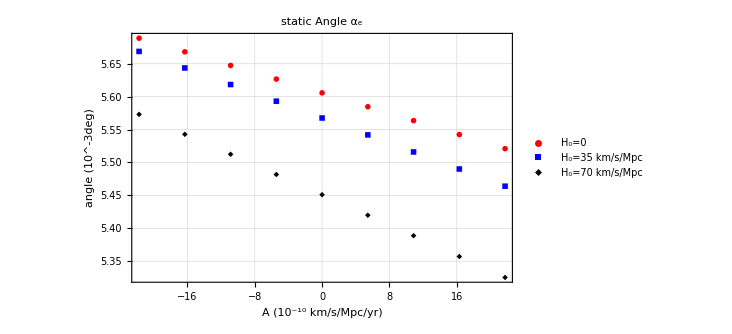

```mathematica
(*Static Bending angle*)
ListPlot[{Table[{1.08711*(5n-25),10^3*(Subscript[ψ, stat][[1,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, stat][[2,n]])},{n,1,9}],Table[{1.08711*(5n-25),10^3*(Subscript[ψ, stat][[3,n]])},{n,1,9}]
},AxesLabel->{"A (10^-10 km/s/Mpc/yr)","angle  (10^-3deg)"},(*,PlotMarkers->Automatic,PlotStyle->Black,*)PlotLabel->"static Angle α_e" ,PlotLegends->Placed[{"H_0=0","H_0=35 km/s/Mpc","H_0=70 km/s/Mpc","H_0=105 km/s/Mpc"},{0.9,.8}], PlotMarkers->{Automatic,Small},PlotStyle->{Red,Blue,Black},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed],Frame->True]
```